```mathematica
Δ=1;Manipulate[Plot[(ω-2Δ)/ω γ/(ω^2+γ^2)HeavisideTheta[ω-2Δ],{ω,0,10}],{γ,0.000001,50}]
```

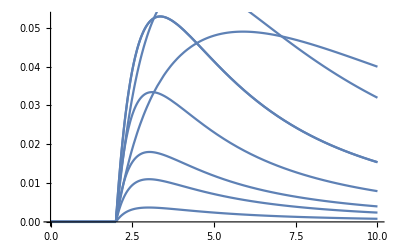

```mathematica
Δ=1;Show[Table[Plot[(ω-2Δ)/ω γ/(ω^2+γ^2)HeavisideTheta[ω-2Δ],{ω,0,10}],{γ,{2,0.1,0.3,0.5,1,2,5,10}}]]
```

```mathematica
Δ=.;Solve[D[α(ω-2Δ)/ω γ/(ω^2+γ^2),ω]==0,ω]//FullSimplify
```

{{ω→Δ-(2^(1/3) Δ^2)/((-γ^2 Δ-2 Δ^3+√(γ^2 Δ^2 (γ^2+4 Δ^2)))^(1/3))-((-γ^2 Δ-2 Δ^3+√(γ^2 Δ^2 (γ^2+4 Δ^2)))^(1/3))/2^(1/3)},{ω→Δ+((-2)^(1/3) Δ^2)/((-γ^2 Δ-2 Δ^3+√(γ^2 Δ^2 (γ^2+4 Δ^2)))^(1/3))+(-γ^2 Δ-2 Δ^3+√(γ^2 Δ^2 (γ^2+4 Δ^2)))^(1/3) Root0.397-0.687 ⅈRoot[1+2 #1^3&,2]0.3968502629920499},{ω→Δ+(-1/2)^(1/3) (-γ^2 Δ-2 Δ^3+√(γ^2 Δ^2 (γ^2+4 Δ^2)))^(1/3)+(Δ^2 Root0.630-1.09 ⅈRoot[2+#1^3&,2]0.6299605249474366)/((-γ^2 Δ-2 Δ^3+√(γ^2 Δ^2 (γ^2+4 Δ^2)))^(1/3))}}

```mathematica
(ω-Δ)γ/(ω^2+γ^2)/.(ω->Δ+√(γ^2+Δ^2))//FullSimplify
```

(-Δ+√(γ^2+Δ^2))/(2 γ)

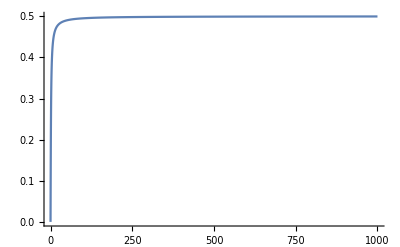

```mathematica
Δ=1;Plot[(-Δ+√(γ^2+Δ^2))/(2 γ),{γ,0,1000},PlotRange->All]
```